```mathematica
randomPoints=RandomReal[{0,5},50] ;(*10 willekeurige punten in[0,5]*)
f[z_]:=1/(1-z);
pointValues=Table[{z,f[z]},{z,randomPoints}];
```

```mathematica
pointValues
```

{{2.61646,-0.618636},{2.58098,-0.632518},{0.305747,1.4404},{2.69837,-0.5888},{0.7982,4.95539},{2.94146,-0.515076},{0.13521,1.15635},{3.65715,-0.376343},{2.52385,-0.656232},{1.08005,-12.4919},{4.73536,-0.267712},{3.88967,-0.34606},{2.5456,-0.647},{3.25825,-0.442821},{3.42657,-0.412104},{0.213079,1.27078},{0.815564,5.42194},{3.63914,-0.378912},{4.62409,-0.275931},{2.24808,-0.801229},{1.34794,-2.87406},{1.8852,-1.12969},{0.337185,1.50872},{4.73686,-0.267604},{1.68942,-1.45049},{2.17347,-0.852176},{0.650165,2.85849},{2.01492,-0.985296},{3.76494,-0.361672},{0.0926822,1.10215},{0.556928,2.25697},{0.762491,4.21037},{1.36484,-2.74096},{3.42154,-0.412961},{3.0328,-0.491931},{1.0909,-11.0011},{3.56161,-0.39038},{4.51215,-0.284726},{2.25139,-0.799111},{0.586589,2.4189},{1.99296,-1.00709},{4.65598,-0.273525},{1.1332,-7.50733},{4.75209,-0.266518},{1.76412,-1.3087},{1.13248,-7.54821},{0.619876,2.63072},{4.36301,-0.297352},{0.802577,5.06526},{3.54479,-0.39296}}

```mathematica
graad=20;
reeks[z_,graad_]:=Sum[a[n] z^n, {n,0,graad}];
fit=FindFit[pointValues,reeks[z,graad],Table[a[n],{n,0,graad}],z];
reeksMetCoefficients[z_]:=reeks[z]/.fitMin
fitMax=FindFit[pointValues,reeks[z,graad+5],Table[a[n],{n,0,graad+5}],z];
reeksMetCoefficientsMax[z_]:=reeks[z]/.fitMax
reeksMetCoefficients[z_]:=Abs[reeksMetCoefficientsMax[z]-reeksMetCoefficientsMin[z]];
```

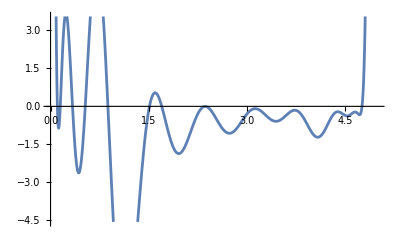

```mathematica
Plot[reeksMetCoefficients[z],{z,0,5}];
Plot[reeksMetCoefficientsMin[z],{z,0,5}]
```

## Opnieuw

```mathematica
randomPoints=RandomReal[{0,5},50]; (*50 willekeurige punten in[0,5]*)
f[z_]:=1/(1-z);
pointValues=Table[{z,f[z]},{z,randomPoints}];
graad=200;
reeks1[z_,graad_]:=Sum[a[n] z^n,{n,0,graad}];
fit1=FindFit[pointValues,reeks[z,graad],Table[a[n],{n,0,graad}],z];
reeksMetCoefficients1[z_]:=reeks[z,graad]/. fit1
reeks2[z_,graad_]:=Sum[a[n] z^n,{n,0,graad+5}];
fit2=FindFit[pointValues,reeks[z,graad+5],Table[a[n],{n,0,graad+5}],z];
reeksMetCoefficients2[z_]:=reeks[z,graad+5]/. fit2
reeksMetCoefficients[z_]:=reeksMetCoefficients2[z]-reeksMetCoefficients1[z];

(*Definieer een reeks testpunten*)testPoints=Range[0,5,0.01];

(*Bereken de functiewaarden op de testpunten*)
reeksValues=Table[{z,reeksMetCoefficients[z]},{z,testPoints}];

(*Definieer een drempelwaarde*)
drempel=35; (*Pas deze waarde aan naar behoefte*)

(*Identificeer de punten waarvan de functiewaarde boven de drempel ligt*)
puntenBovenDrempel=Select[reeksValues,#[[2]]>drempel&];

(*Haal de corresponderende z-waarden op*)
puntenZ=puntenBovenDrempel[[All,1]];

(*Print de resultaten*)
puntenZ
```

Power::indet: Indeterminate expression 0.^0 encountered.

General::munfl: 0.01^154 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.01^155 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.01^156 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{4.36,4.37,4.38,4.39,4.4,4.41,4.42,4.43,4.44,4.45,4.46,4.47,4.48,4.49,4.5,4.51,4.55,4.56,4.57,4.58,4.59,4.6,4.61,4.62,4.63,4.64,4.65,4.66,4.67,4.68,4.69,4.7,4.71,4.72,4.73,4.74,4.75,4.76,4.77,4.78,4.79,4.82,4.83,4.84,4.85,4.86,4.87,4.88,4.89,4.9,4.91,4.92,4.93}